# Boats Boats Goats Goats

## Inputs and Example Plot

5000

{0,0}

10

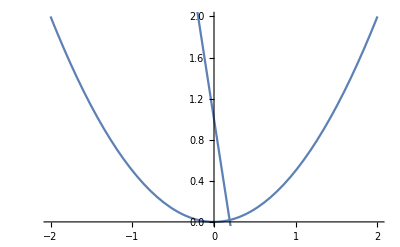

```mathematica
BoatCurve = 2*Abs[x/2]^2;
HeelAngle = 101;      (*degrees*)
BoatDensity = 300; (*kg/m^3*)
MassBalast = 5000   (*kg*)
COBallast = {0,0}
BoatLength = 10

Show[Plot[BoatCurve, {x,-2,2}],Plot[Tan[HeelAngle Degree]*(x-0)+1, {x, -2,2}]]
```

## Calculating Buoyancy point

{0,32/35}

2.50384

{0.908748,1.3074}

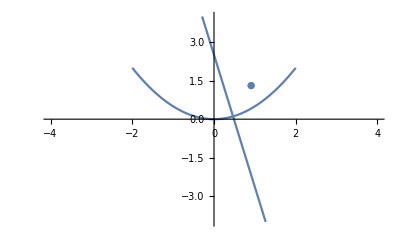

```mathematica
boat = ImplicitRegion[BoatCurve<y<2&&-2<x<2&&0<y<2,{x,y}];
water = If[HeelAngle == 90, ImplicitRegion[x>0&&-2<x<2&&-2<y<4,{x,y}],
If[HeelAngle<90,ImplicitRegion[y<Tan[HeelAngle Degree]*(x+d)&&-2<x<2&&-2<y<4,{x,y}], ImplicitRegion[y>Tan[HeelAngle Degree]*(x)+d&&-2<x<2&&-2<y<4,{x,y}]]];

under = RegionIntersection[boat,water];

mass = BoatLength*Integrate[BoatDensity,{x,y}∈boat]+MassBalast;
disp = BoatLength*Integrate[1000,{x,y}∈under];
com = 1/mass*(Integrate[BoatDensity*{x,y},{z, 0 ,10}, {x, -2, 2},{y, BoatCurve, 2}]+MassBalast*COBallast)
Force = mass*9.8;


(*Plot[disp,{d,-2,4}]*)
waterline = Solve[disp==mass,d,Reals];
draft = N[d/.waterline[[1]]]

cob = 10*Integrate[1000*{x,y},{x,y}∈under]/disp;
cob = cob/.{d->draft}

Show[Plot[Tan[HeelAngle Degree]*x+draft, {x, -3,3}, PlotRange->{{-4, 4},{-4,4}}], Plot[BoatCurve, {x,-2,2}], ListPlot[{cob}]]

(*Show[RegionPlot[{water/.{d->draft},boat,under/.{d->draft}},AspectRatio->Automatic],ListPlot[{cob/.{d->draft}, com}]]*)
```

## Calculating Torque and AVS

```mathematica
cob = cob /.{d->draft};

r = {(cob[[1]]-com[[1]]),(cob[[2]]-com[[2]]), 0};
f = FromPolarCoordinates[{Force, (90 -HeelAngle) Degree}];
F = {f[[1]], f[[2]], 0};


T = Cross[r, F]

(*Graphics3D[Arrow[{{0,0,0},T, {0,0,0},r, F}]]*)
```

{0.,0.,-147468.}